## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
signature = randomSignature[3, 3, 2]
```

{{2,2},{1,1}}→{{2,3}}

```mathematica
signature={{2,2}}->{{4,2}}
```

{{2,2}}→{{4,2}}

```mathematica
init = Array[Function[1],signature[[1]][[1]]]
```

{{1,1},{1,1}}

```mathematica
rule=randomRule[signature]
```

{{1,2},{3,2}}→{{1,4},{1,5},{4,6},{3,6}}

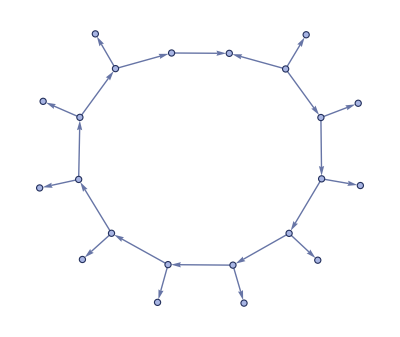

```mathematica
wm[rule, init, steps, "FinalStatePlot"]
```

```mathematica
gOrig = wm[rule, init,steps,"FinalState"]
```

{{1,2},{1,3},{2,5},{2,6},{5,8},{5,9},{8,11},{8,12},{11,14},{11,15},{14,17},{14,18},{17,20},{17,21},{20,23},{20,24},{23,26},{23,27},{26,29},{26,30},{29,31},{1,31}}

## Mutations

```mathematica
rule = {rule}
```

{{{1,2},{3,2}}→{{1,4},{1,5},{4,6},{3,6}}}

```mathematica
selectElement[rule_]:=
Module[{replacement, side, edge, vertex, x},
replacement=RandomInteger[{1, Length[rule]}];
x = rule[[replacement]];
side = RandomInteger[{1, 2}];
x = x[[side]];
edge = RandomInteger[{1, Length[x]}];
x = x[[edge]];
vertex = RandomInteger[{1, Length[x]}];
{replacement, side, edge, vertex}
]
```

```mathematica
maxElement[rule_]:=Max[Flatten[List@@@rule]]
```

```mathematica
replaceRandomElement[rule_]:=
ReplacePart[rule, selectElement[rule]->RandomInteger[{1,maxElement[rule]}]]
```

```mathematica
rule
```

{{{1,2},{3,2}}→{{1,4},{1,5},{4,6},{3,6}}}

```mathematica
newRule=replaceRandomElement[rule]
```

{{{1,2},{3,2}}→{{1,4},{1,5},{4,6},{3,6}}}

```mathematica
evolution = wm[newRule, init, steps]
```

WolframModelEvolutionObject[…]

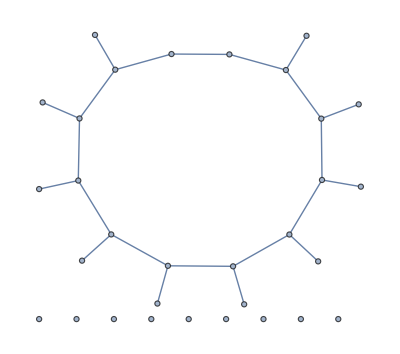

```mathematica
Graph@evolution["FinalState"]
```

```mathematica
evolution["VertexCountList"]
```

{1,4,6,8,10,12,14,16,18,20,22}

```mathematica
graphDimension[graph_] := 
 	ResourceFunction["WolframHausdorffDimension"][graph, All, "AllDimensions","VertexMethod" -> Max]
```

```mathematica
components =WeaklyConnectedComponents[g]
```

{{1,2,3,31,5,6,29,8,9,26,11,12,23,30,14,15,20,27,17,18,24,21},{28},{25},{22},{19},{16},{13},{10},{7},{4}}

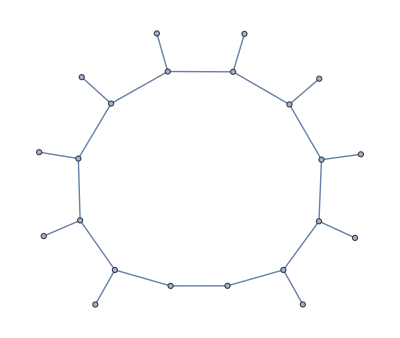

```mathematica
connectedG=Subgraph[g, components[[1]]]
```

```mathematica
graphDimension[connectedG]
```

1.66024